# Practicals 3 date: 09/02/23

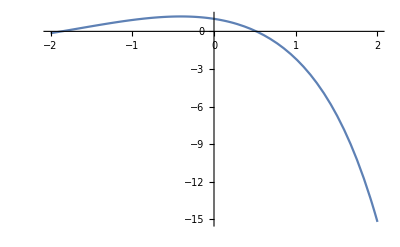

```mathematica
newtonRaphson[f_, p0_, n_] :=Module[{},pold=N[p0];
i=1;
df[x_]=D[f[x],x];
While[i≤n,
pnew=N[pold-N[f[pold]]/N[df[pold]]];
Print[i, "    ", pnew];
i++;
pold=pnew];
Print[" Root = " , pnew]]

f[x_] = Cos[x]-x*Exp[x];
Plot[f[x], {x, -2, 2}]
```

```mathematica
newtonRaphson[f, 0, 5]
```

1    1.

2    0.653079

3    0.531343

4    0.51791

5    0.517757

Root = 0.517757

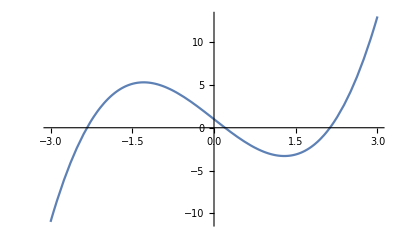

```mathematica
f[x_] = x^3-5x+1;
Plot[f[x], {x,-3, 3}]
```

```mathematica
newtonRaphson[f, 0, 5]
```

1    0.2

2    0.201639

3    0.20164

4    0.20164

5    0.20164

Root = 0.20164

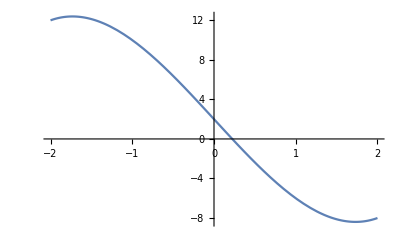

1    0.222222

2    0.223462

3    0.223462

4    0.223462

5    0.223462

Root = 0.223462

```mathematica
f[x_] = x^3-9*x +2;
Plot[f[x], {x, -2,2}]
newtonRaphson[f, 0, 5]
```